# Blatt 4 - Jonas Neundorf und Jan Skottke

## Konstanten

```mathematica
constants = {b-> 1 (*T*), u0 -> 100000(*V*), c-> 300000000(*m/s*), q-> 1.602*10^-19(*C*), m -> 1.673*10^-27(*kg*)}
```

{b→1,u0→100000,c→300000000,q→1.602×10^-19,m→1.673×10^-27}

## Formeln:

Zyklotronfrequenz:

```mathematica
ωc=(q*b)/m //.constants;
```

Erstelle ein Modul, welches die Energie, den Radius und die Phasendifferenz berechnet, die bei einem Durchlauf hinzugewonnen wird.

```mathematica
blub[{w_, r_, ϕ_, ωrf_, n_ (* wird nicht für die Berechnung gebraucht, aber als Index in der Auswertung *) }] := Module[{γ, uhf,ϕ2, w2,radius,vmom},
(* Hier wird ausgenutzt, dass t = Pi/Subscript[ω, n] ist. 
γ wird aus der Bewegungsenergie bestimmt *)
ϕ2 =ϕ + (ωrf*γ*(Pi/ωc)-Pi)//.Solve[w*q== (γ-1)*m*c^2, γ][[1,1]];
uhf = -u0 Cos[ωrf*Pi*(γ/ωc) + ϕ]//.Solve[w*q== (γ-1)*m*c^2, γ][[1,1]]; (* momentane Beschleunigungsspannung*)
w2 = w + uhf//.constants;
vmom:=√((2/m)*q*w);
radius = (γ*vmom*m)/(q*b) //.Solve[w*q== (γ-1)*m*c^2, γ][[1,1]]//.constants;
Return[{w2 (* eV *), radius (* m *), ϕ2 (* radiant *), ωrf (*1/s *), n+1}]
]
```

Anmerkung :  es ist vielleicht nicht so elegant, das Solve bei jedem Schritt immer wieder zu machen. Aber wenn es funktioniert ... Geschmacksache...

Erstelle ein Modul, welches für n Halbperioden und beliebiges ωrf die Energie, den Radius und die Phasendifferenz berechnet:

```mathematica
blub2[{ωrf_,nend_}] := Module[{n,result},
n=0;
(* Das Teilchen startet in Ruhe zur Zeit 0 *)
result =NestList[blub,{0,0,0,ωrf,n},nend] //.constants;
Return[result]
]
```

```mathematica
data = blub2[{ωc,300}];
```

Gebe den Eintrag mit der höchsten Energie aus:

```mathematica
SortBy[data, First][[Length[data]]]
```

{7.73531×10^6,0.405194,1.54721,9.57561×10^7,101}

## Plots:

Man sieht, dass die Energie zunächst linear mit der Zahl der Halbperioden ansteigt, bevor der Anstieg abflacht. Nach 101 Halbperioden beträgt der Phasenunterschied π/2, sodass das Proton jetzt abgebremst wird, bevor es nach gut 200 Halbperioden sich in entgegengesetzter Richtung bewegt.

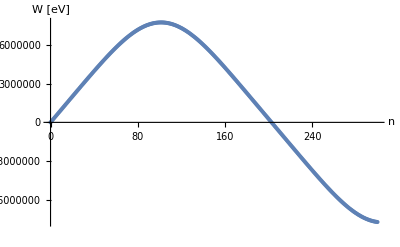

```mathematica
ListPlot[ data[[All, {5, 1}]], AxesLabel->{"n", "W [eV]"}]
```

Der Phasenunterschied ϕ nimmt erst ab, wenn das Proton sich in die entgegengesetzte Richtung bewegt.

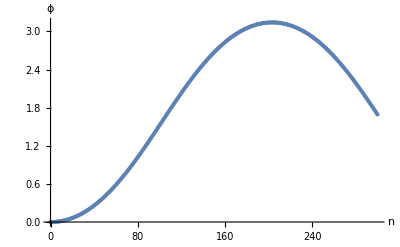

```mathematica
ListPlot[ data[[All, {5, 3}]], AxesLabel->{"n", "ϕ"}]
```

Variiere ωrf um ωc:

```mathematica
Manipulate[ListPlot[blub2[{ωc*α, 150}][[All, {5, 1}]], AxesLabel->{"n", "W"}],{α, 0.99, 1.01, 0.00025}]
```

Die höchste Energie wird bei bei ωrf = 0.9945 ωc erreicht.

Anmerkung : die  140 Halbumläufe reichen bei optimaler Verstimmung nicht um das Maximum zu erreichen..